## Fourier Series and Transforms -- an Introduction

In math, you're used to the notion that any periodic function can be represented as an infinite series of sines and cosines, with each sine and cosine having a different frequency.  This is, of course the idea behind Fourier series.

Let's start with an example to refresh your memory.  Consider a sawtooth wave.  Below we've plotted one with a period of 2 π.

```mathematica
Wave[x_,L_]:=SawtoothWave[{-1,1}, x/L]
```

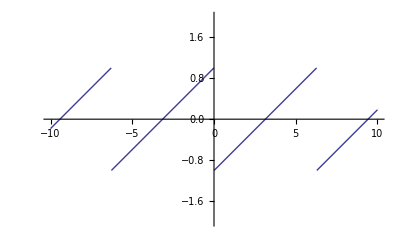

```mathematica
Plot[Wave[x, 2π], {x, -10, 10}, PlotRange->{-2, 2}, AxesLabel->{x}]
```

Since the sawtooth wave is periodic, we can expand it as a Fourier series.  The series consists of an infinite series of sines and cosines, but we can get a pretty good approximation by just taking the first few terms.  Plotted below in dark blue/purple is the exact sawtooth function, and shown in dark pink is our approximation to it.

```mathematica
ApproximateWave[x_,L_]:=FullSimplify[Expand[FourierSeries[Wave[x,L], x, 8]]]
```

```mathematica
ApproximateWave[x,2π]
```

-(2 (7 (60 Sin[x]+30 Sin[2 x]+20 Sin[3 x]+15 Sin[4 x]+12 Sin[5 x]+10 Sin[6 x])+60 Sin[7 x])+105 Sin[8 x])/(420 π)

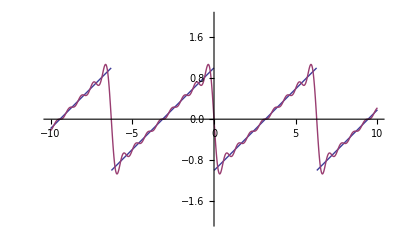

```mathematica
Plot[{Wave[x,2π],%}, {x, -10, 10}, PlotRange->{-2, 2}, AxesLabel->{x}]
```

Plotting the function and its Fourier series like we did above is one way to understand Fourier series.  Another way is to plot the "strength" of each sine (or cosine) term as a function of the frequency/wavenumber (k).  This is shown in the spiky plot *below*.  Let's step through how to read a plot like this.  The spike at k=5 has a height of about 0.06.  This means that the sin(5 x) term in the Fourier series has an amplitude of 0.06 multiplied in front of it.  Similarly, the spike at k=3 has a height of about 0.11, which means the sin(3x) term has an amplitude of 0.11.  In words, what this Fourier representation (i.e. this graph of spikes) is telling us is that if we want to assemble a sawtooth wave from a series of sines and cosines, we need to add together sine and cosine "ingredients" in various amounts.  In this case, we need 0.11 parts of sin(3x), 0.06 parts of sin(5x) and so on.  The fact that the graph is a series of spikes means that we don't need any "in-between" frequencies like sin(1.5x).  The Fourier representation contains all the information contained in the original function, because given this "recipe" I can reconstruct the function by adding together the "ingredients" in the right amoutns.  Incidentally, the graph below also "explains" why we can get a pretty decent approximation to our original function by just considering the first few terms in the Fourier series.  Notice that the amplitude of the function is large for small wavenumbers k and gets smaller as we go to larger and larger k.  This means that the very high frequency terms (the highest "k" terms) in the Fourier series contribute only very small quantities to the sum, and so we don't lose too much be ignoring them.

There's a tendency to think that the squiggly graph of the sawtooth shown above as "the" function, and the spiky Fourier representation below as some silly way of doing things, but both are valid.  We can think of any function as some abstract thing that we can choose to represent as a function in "real space x" (the wiggly function above) or as a function in "fourier space k" (the spiky function below).  Both are equally valid ways of thinking about a function, and which representation is more "natural" is just a matter of application.  For instance, if I'm trying to describe to you what a set of ocean waves looks like, it makes sense for me to use a real space representation, where waves are actually "wavy".  On the other hand, our auditory sensations operate in Fourier space -- when you hear a musical chord, what your brain perceives isn't a waveform, but rather a mixture of frequencies, i.e. pitches ("Ah yes...I hear about equal mixtures of 'A', 'C#' and 'E'").

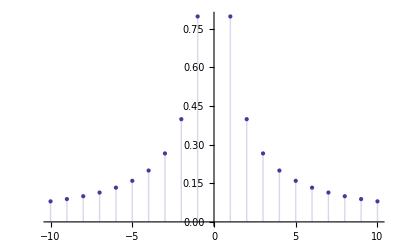

```mathematica
FourierCoefficient[Wave[x, 2 π], x, n,FourierParameters->{0,-1}];
DiscretePlot[Abs[%],{n,-10,10},PlotRange->All, AxesLabel->{k}]//Quiet
```

Let's do another example to get some intution for this.  I'd like to compare two sawtooth waves and their Fourier representations.  Shown below are two sawtooth waves, one with a period of 2 π (in blue) and one with a period of π/2 (in red).

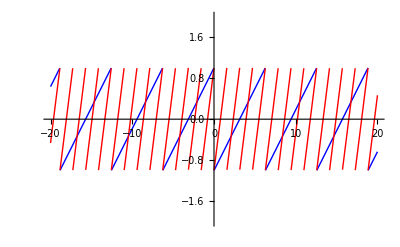

```mathematica
Plot[{Wave[x, 2 π],Wave[x, π/2]} , {x, -20, 20}, PlotRange->{-2, 2},PlotStyle->{{RGBColor[0,0,1]},{RGBColor[1,0,0]}}]
```

We can once again approximate the waves using Fourier series, and below we've plotted things in real space.

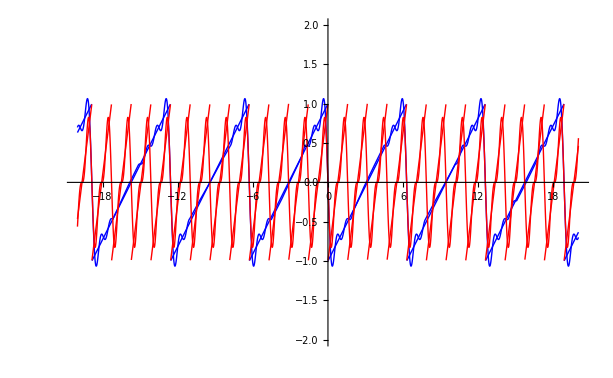

```mathematica
{Wave[x, 2 π], ApproximateWave[x,2 π], Wave[x, π/2],ApproximateWave[x, π/2]};
Plot[%, {x, -20, 20}, PlotRange->{-2, 2},PlotStyle->{{RGBColor[0,0,1]},{RGBColor[0,0,1]},{RGBColor[1,0,0]},{RGBColor[1,0,0]}}]
```

Here is the Fourier representation:

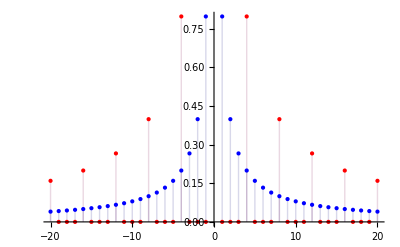

```mathematica
{FourierCoefficient[Wave[x, 2 π], x, n,FourierParameters->{0,-1}],FourierCoefficient[Wave[x,  π/2], x, n,FourierParameters->{0,-1}]};
DiscretePlot[Abs[%],{n,-20,20},PlotRange->All, AxesLabel->{k}, PlotStyle->{{RGBColor[0,0,1]},{RGBColor[1,0,0]}}]//Quiet
```

This is interesting! Remember how this graph tells us what mixtures of sinusoids to use, and notice how function with the shorter period (red) doesn't "use" all of the wavenumbers available to it.  In other words, whereas to construct the shorter period (red) wave, we only need to use sin(4x), sin(8x), sin(12x), and so on, we need to use a more complete set of sines (sin x, sin 2x, sin3x, ...) in order to construct the longer period (blue) wave.  To see if this is mere coincidence, we can repeat this experiment for waves of even shorter periods:

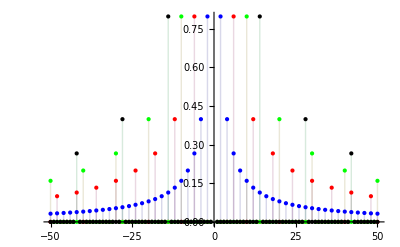

```mathematica
{FourierCoefficient[Wave[x, π], x, n,FourierParameters->{0,-1}],
FourierCoefficient[Wave[x, π/3], x, n,FourierParameters->{0,-1}],
FourierCoefficient[Wave[x, π/5], x, n,FourierParameters->{0,-1}],
FourierCoefficient[Wave[x, π/7], x, n,FourierParameters->{0,-1}]};

DiscretePlot[Abs[%],{n,-50,50},PlotRange->All, AxesLabel->{k}, PlotStyle->{{RGBColor[0,0,1]},{RGBColor[1,0,0]}, {RGBColor[0,1,0]}, {RGBColor[0,0,0]}}]//Quiet
```

Shown above are the Fourier representations of sawtooth waves of period π/7 (in black), π/5 (in green), π/3 (in red) and π (in blue).  It's true! The shorter the period, the sparser the Fourier representation.  Conversely, the longer the period of the function we're trying to represent, the denser the Fourier representation -- the spikes populate the gaps more completely, and as a whole the tall spikes are more "centrally condensed" towards the smaller values of k.  This makes a lot of sense intuitively if you think about what a Fourier representation is.  Remember that the graph of spikes is a recipe that tells us how much of each sine to add to our mixture that becomes the original function, and that the smaller the wave number of a sine wave, the longer its period (e.g. sin x has a period of 2 π whereas sin 2x --which has a larger wavenumber of 2 -- has a period of π).  What this pattern tells us is that if my original function has a long period, then to reconstruct it with sines and cosines I need to use sinusoids with longer periods i.e. smaller wavenumber k.  Thus, the more "stretched out" a function is in real space (the longer its period in real space), the more centralized/"squished" it is in Fourier space.

Now here's the big conceptual leap.  Let's suppose we go crazy with this exercise, and keep increasing the period of the function that we're find Fourier series for.  As we keep doing this, the spikes populate the k-axis in Fourier space more and more densely (imagine the blue dots in the plot above getting more and more squished together so that they're like trees in a thick forest).  What if we increase the period of the wave to infinity? Huh? What does it mean to have a period equal to infinity? A period, remember, is how far we have to go in real space before the wave repeats itself.  If the period is infinity, then it takes infinitely long before the wave repeats itself, which is another way of saying that it never repeats itself.  A "periodic" function with an infinite period is just an aperiodic function.

So what does happen to the Fourier representation as we increase the period to infinity? As we increase the period of the wave to infinity, the spikes get closer to closer together, and what used to be a discrete set of spikes gets infinitely squished together and get so dense that they form a continuous function.  All the gaps between the spikes disappear as the limit to infinity is taken.  What this means is that whereas a periodic function can be represented by a discrete set of sines and cosines (e.g. sin x, sin 2x, sin 3x, and so on, but not anything like sin 1.3x), an aperiodic function (i.e. functions in general) can only be formed from sums of sines and cosines if we add together a continuous mixture (i.e. we need not only sin x and sin 2x, but also sin 1.5x, sin 1.01x, sin 1.0001x -- everything).

What we've just described is the idea behind Fourier Transforms.  The continuous function that came out of squishing the spikes together is known as the Fourier transform of the original function.

Let's look at a few examples.  We'll start with a sine wave:

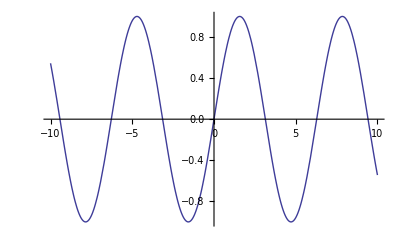

```mathematica
Plot[Sin[x], {x, -10, 10}, AxesLabel->{x}]
```

Now we take the Fourier transform:

```mathematica
FourierTransform[Sin[x],x,k,FourierParameters->{0,-1}]
```

-ⅈ √(π/2) DiracDelta[-1+k]+ⅈ √(π/2) DiracDelta[1+k]

What are we to make of this? Recall that the Fourier transform is a function that tells us how much of each type of sinusoid to take.  This Fourier transform consists of delta functions at k=1 and k= -1.  This means that to reconstruct sin x, we just need k= +/-1 sinusoids (sin x and sin(-x) )and nothing else, which makes sense -- the point of a Fourier series/transform is to represent a function in terms of sinusoids, and if the original function is already a sine then the only ingredient we need from our arsenal of sines and cosines is "itself".  (Don't worry about the fact that we need both sin x and sin (-x), and the funny imaginary amplitudes -- those are just artifacts of the fact that Fourier transforms are defined using complex exponentials instead of sines and cosines).

Let's try another example.  What about a constant?

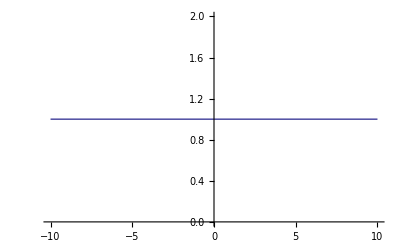

```mathematica
Plot[1, {x, -10, 10}, AxesLabel->{x}]
```

```mathematica
FourierTransform[1,x,k,FourierParameters->{0,-1}]
```

√(2 π) DiracDelta[k]

This time we get a delta function centered at k=0, which means that our recipe for reconstructing the constant function y =1 is to take a sinusoid with wavenumber k=0 i.e. a sinusoid that doesn't vary at all.  That sounds like a constant! (Again, don't worry about the constant factor up front).

## Examples of Fourier Series and Transforms

### Fourier Series: Superposing Plane Waves makes a Sharply Peaked Function

```mathematica
Manipulate[
{Plot[Re[1/(√(2π nMax))∑_(n=1)^nMax ⅇ^(ⅈ n x)],{x,π,3*π},PlotRange->All],
Plot[Abs[1/(√(2π nMax))∑_(n=1)^nMax ⅇ^(ⅈ n x)]^2,{x,π,3*π},PlotRange->All]}
,{nMax,1,40,1}]
```

### Fourier Transforms: A Discontinuous Example (One Small Step for a Wavefunction)

```mathematica
(* In what follows, it will be helpful to alert Mathematica to which of our 
variables are real, positive, etc.  This helps keep MMatica from panicing too often. *)
$Assumptions={ψo∈Reals,ψo>0,x∈Reals,xo∈Reals,k∈Reals,ko∈Reals,L∈Reals,L>0,ϵ∈Reals,ϵ>0,Λ∈Reals,Λ>0,ℏ∈Reals,ℏ>0};
```

General::spell: New symbol name "ψo" is similar to existing symbols {ψ, ψr, ψz} and may be misspelled.

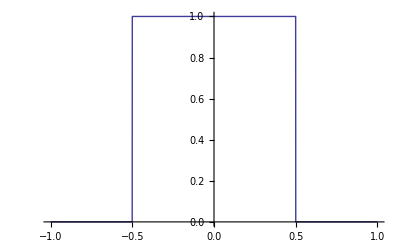

```mathematica
(* So!  First we need to build a "step function" function.
Step[ϵ,x] defines a step of width ϵ around the origin.
It is normalized so that it's norm-squared integrates to 1. *)
Step[ϵ_,x_]=(UnitStep[x+ϵ/2]-UnitStep[x-ϵ/2])/(√ϵ);
Plot[Step[1,x],{x,-1,1},Exclusions->None]
```

```mathematica
(* Now let's build a wavefunction which is a plane wave over an interval of
length L centered on the point xo. *)
Clear[ψo,ψ];
ψ[L_,xo_,ko_,x_]:=ψo Step[L,x-xo] ⅇ^(ⅈ ko (x-xo));
```

```mathematica
(* We can fix ψo so that ψ is correctly normalized: *)
ψo=1/√(∫_(-∞)^∞ Abs[1/ψo ψ[L,xo,ko,x]]^2 ⅆx)//Simplify
```

1

```mathematica
(* Let's verify that ψ is correctly normalized: *)
∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 ⅆx
```

1

```mathematica
(* Now let's compute the fourier transform ψ̃(k) *)
(* Note that Mathematica uses a slightly different default convention for their FourierTransform:
    f̃(k)=1/(√(2 π))∫_(-∞)^∞ f(x)e^ikx ⅆx
To get MMatica to use 8.04 conventions, you need to add
    FourierParameters->{0,-1}
to the FourierTransform function call.  We'll do that below.
 *)

ψ̃[L_,xo_,ko_,k_]=FourierTransform[ψ[L,xo,ko,x],x,k]//Simplify
```

(ⅇ^(ⅈ k xo) √(2/π) Sin[(k+ko)/2])/(k+ko)

```mathematica
(* To get a sense for what this looks like for various values of the width L and the momentum ko,
let's Plot ψ and ψ̃ , using Manipulate to allow us to vary the width L. 
Note: to make the plots bigger, click inside the graph*)
Manipulate[{
Plot[Abs[ψ[L,xo,ko,x]]^2,{x,-10,10},PlotRange->All,Exclusions->None],
Plot[Re[ψ̃[L,xo,ko,k]],{k,-100,100},PlotRange->All]
},{L,10,0.1},{xo,0,10},{ko,0,50}]
```

```mathematica
(* What are the expectation values for x and x^2? What's the uncertainty Δx? 
For simplicity, let's pick a step centered on the origin, xo = 0.  *)
Subscript[x, avg]=∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 xⅆx
Subscript[x^2, avg]=∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 x^2 ⅆx
Δx=√(Subscript[x^2, avg]-Subscript[x, avg]^2)//Simplify
```

xo

1/12 (1+12 xo^2)

General::spell1: New symbol name "Δx" is similar to existing symbol "Δ" and may be misspelled.

1/(2 √3)

```mathematica
(* What about p and p^2? What's the uncertainty Δp? *)
Subscript[p, avg]=∫_(-∞)^∞ Abs[ψ̃[L,xo,ko,k]]^2 ℏ kⅆk
Subscript[p^2, avg]=∫_(-∞)^∞ Abs[ψ̃[L,xo,ko,k]]^2 ℏ^2 k^2 ⅆk
Δp=√(Subscript[p^2, avg]-Subscript[p, avg]^2)//Simplify
```

∫_(-∞)^∞ (2 ⅇ^(-2 Im[k xo]) k ℏ Abs[Sin[(k+ko)/2]/(k+ko)]^2)/π ⅆk

∞ Sign[ℏ]^2

General::spell: New symbol name "Δp" is similar to existing symbols {Δ, Δx} and may be misspelled.

√(∞-(∫_(-∞)^∞ (2 k ℏ Abs[Sin[(k+ko)/2]/(k+ko)]^2)/π ⅆk)^2)

```mathematica
(* So the expectation values for the momentum diverge!!  We should of course have expected that fmor the fact that the wavefunction is discontinuous, but it's nice to see that the momentum-space computation gives the same divergent result. *)
```

### Fourier Transforms: A Continuous but Non-Smooth Example (A Speedbump)

```mathematica
(* Now let's build a wavefunction which is a bump over an interval of
length L centered on the point xo. *)
Clear[ψo,ψ];
ψ[L_,xo_,ko_,x_]:=ψo[L] Step[L,x-xo] ⅇ^(ⅈ ko (x-xo))((L/2)^2-(x-xo)^2);
```

```mathematica
(* We can fix ψo so that ψ is correctly normalized: *)
ψo[L_]=1/√(∫_(-∞)^∞ Abs[1/ψo[L] ψ[L,xo,ko,x]]^2 ⅆx)//Simplify
```

√30

```mathematica
(* Let's verify that ψ is correctly normalized: *)
∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 ⅆx
```

1

```mathematica
(* Now let's compute the fourier transform ψ̃(k) *)
(* Note that Mathematica uses a slightly different default convention for their FourierTransform:
    f̃(k)=1/(√(2 π))∫_(-∞)^∞ f(x)e^ikx ⅆx
To get MMatica to use 8.04 conventions, you need to add
    FourierParameters->{0,-1}
to the FourierTransform function call:
 *)

ψ̃[L_,xo_,ko_,k_]=FourierTransform[ψ[L,xo,ko,x],x,k,FourierParameters->{0,-1}]//FullSimplify
```

(ⅇ^(-1/2 ⅈ (k+ko+2 k xo)) (ⅇ^(ⅈ k) (-2 ⅈ-k+ko)+ⅇ^(ⅈ ko) (2 ⅈ-k+ko)) √(15/π))/(k-ko)^3

```mathematica
(* Notice the much better (ie convergent) large-k behaviour as compared to the previous example.*)
(* To get a sense for what this looks like for various values of the width L and the momentum ko,
let's Plot ψ and ψ̃ , using Manipulate to allow us to vary the width L. 
Note: to make the plots bigger, click inside the graph.  Also, compare with the results from the step function above! *)
Manipulate[{
Plot[Abs[ψ[L,xo,ko,x]]^2,{x,-10,10},PlotRange->All,Exclusions->None],
Plot[Re[ψ̃[L,xo,ko,k]],{k,-50,50},PlotRange->All]
},{L,6,0.1},{xo,0,10},{ko,0,50}]
```

```mathematica
(* What are the expectation values for x and x^2? What's the uncertainty Δx? *)
Subscript[x, avg]=∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 xⅆx
Subscript[x^2, avg]=∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 x^2 ⅆx
Δx=√(Subscript[x^2, avg]-Subscript[x, avg]^2)//Simplify
```

xo

1/28 (1+28 xo^2)

1/(2 √7)

```mathematica
(* What about p and p^2? What's the uncertainty Δp? *)
Subscript[p, avg]=∫_(-∞)^∞ Abs[ψ̃[L,0,0,k]]^2 ℏ kⅆk  (* Note: Setting xo=ko=0 to simplify Mathematica's life. Changes nothing about Δp. *)
Subscript[p^2, avg]=∫_(-∞)^∞ Abs[ψ̃[L,0,0,k]]^2 ℏ^2 k^2 ⅆk
Δp=√(Subscript[p^2, avg]-Subscript[p, avg]^2)//Simplify
```

0

10 ℏ^2

√10 ℏ

```mathematica
(* The uncertainty relation is thus nicely satisfied, *)
Δx Δp
```

√(5/14) ℏ

```mathematica
(* This corresponds to roughly 20% away from the lower bound -- pretty good!  and indeed the wavefunction does look a good bit like a gaussian....*)
%/(ℏ/2)//N
```

1.19523

### Fourier Transforms: A Smooth Approximation to a Step

```mathematica
(* When it comes to computing <p>, however, we run into problems since the wavefunction is not continuous.
In momentum space, this can be traced to the fourier transform failing to die off sufficiently rapidly at large momenta -- indeed, at large k, ψ̃(k) scales like 1/k.  To deal with this let's build a smooth function which approximates the step function: *)
SmoothStep[m_][ϵ_,x_]:=(Tanh[m(x+ϵ/2)]-Tanh[m(x-ϵ/2)])/2 √(m/(ϵ m Coth[ϵ m]-1));
(* That coefficient is chosen to properly normalize the square of the step -- let's check: *)
(* ∫_(-∞)^∞ Simplify[(SmoothStep[Λ][L,x])^2]ⅆx  *)(* Note: Mathematica takes *forever* to compute this; faster to do it by hand. *)
(* As m gets large, SmoothStep reduces to Step, as is easiest to see by ploting both for various values of m: *)
Manipulate[Plot[{Step[1,x],SmoothStep[m][1,x]},{x,-1,1},Exclusions->None],{m,3,200}]
```

```mathematica
(* Now let's repeat all of the above computations, but now with the smooth approximation. 
To begin, let's build a wavefunction which is a plane wave times a SmoothStep of length L at xo:  *)
Clear[ψ,M];
ψ[M_,L_,xo_,ko_,x_]:= SmoothStep[M][L,x-xo] ⅇ^(ⅈ ko (x-xo));
```

```mathematica
(* Note that ψ is correctly normalized because SmoothStep was correctly normalized. *)
(* To check, compute ∫_(-∞)^∞ Abs[ψ[L,xo,ko,x]]^2 ⅆx  *) 
(* Annoyingly this integral takes forever so you're better off doing it by hand. *)
```

```mathematica
(* Now let's compute the fourier transform ψ̃(k) *)
(* Note that Mathematica uses a slightly different default convention for their FourierTransform:
    f̃(k)=1/(√(2 π))∫_(-∞)^∞ f(x)e^ikx ⅆx
To get MMatica to use 8.04 conventions, you need to add
    FourierParameters->{0,-1}
to the FourierTransform function call.
 *)
(* Now, if you just try 

ψ̃[L_,xo_,ko_,k_]=FourierTransform[ψ[L,xo,ko,x],x,k,FourierParameters->{0,-1}]//Simplify

 MMatica barfs, so let's simplify by noting that if
    f̃(k)=1/(√(2 π))∫_(-∞)^∞ f(x)e^-ikx ⅆx
then
   1/(√(2 π))∫_(-∞)^∞ f(ax+b)e^(ⅈ ko(x-xo))e^(-ⅈ k x)ⅆx = 1/(√(2 π))∫_(-∞)^∞ 1/a f(y)e^(ⅈ ko((y-b)/a-xo))e^(-i k/a(y-b))ⅆy = e^(i(k-ko)b/a-ikoxo)/a f̃((k-ko)/a)
Now, 
		ψ=1/2 ⅇ^(ⅈ ko (x-xo)) √(M/(-1+L M Coth[L M])) (-Tanh[M (-L/2+x-xo)]+Tanh[M (L/2+x-xo)])
ie
	ψ = 1/2 √(M/(-1+L M Coth[L M])) (-ⅇ^(ⅈ ko (x-xo))Tanh[M x - M(xo+L/2)]+ ⅇ^(ⅈ ko (x-xo))Tanh[M x - M(xo-L/2)])
thus, if the fourier transform of Tanh[x] is f̃(k), then
	ψ̃ = 1/2 √(M/(-1+L M Coth[L M]))(-e^(-i(k-ko)(xo+L/2)-ikoxo)/M f̃((k-ko)/M)+e^(-i(k-ko)(xo-L/2)-ikoxo)/M f̃((k-ko)/M))
so: what's the fourier transform of Tanh[x]? 
*)
FourierTransform[Tanh[x],x,k,FourierParameters->{0,-1}]
```

-ⅈ √(π/2) Csch[(k π)/2]

```mathematica
(* Plugging this into our expression and simplifying a bit gives:  *)
ψ̃[M_,L_,xo_,ko_,k_] =  √(π/2)√(M/(-1+L M Coth[L M]))ⅇ^(-ⅈ k xo)/M Sin[(L(k-ko))/2]Csch[π/2((k-ko)/M)];
```

```mathematica
(* To get a sense for what this looks like for various values of the width L and the momentum ko,
let's Plot ψ and ψ̃ , using Manipulate to allow us to vary the width L, the position and momentum xo and ko, and the sharpness of the step, M.  Note in particular what happens to the support of ψ̃ as the step gets sharp, M->∞. 
Note: to make the plots bigger, click inside the graph*)
Manipulate[{
Plot[Abs[ψ[M,L,xo,ko,x]]^2,{x,-10,10},PlotRange->All,Exclusions->None],
Plot[Re[ψ̃[M,L,xo,ko,k]],{k,-100,100},PlotRange->All]
},{L,1,0.1},{xo,0,10},{ko,0,50},{M,3,400}]
```